```mathematica
ClearAll["Global`*"]

zms = Import[NotebookDirectory[]<>"zms.mx"];
wvals = Import[NotebookDirectory[]<>"wvals.mx"];
Frhos = Import[NotebookDirectory[]<>"Frhos.mx"];
ma1s = Import[NotebookDirectory[]<>"ma1vaues.mx"];
fa1s = Import[NotebookDirectory[]<>"fa1s.mx"];
```

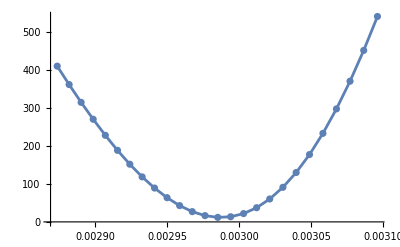

```mathematica
cma1 = (ma1s - 1230)^2/40;
cFrhos = (Frhos - 345)^2/8;
cfa1s = (fa1s - 433)^2/13;

chisq = Flatten[cma1 + cFrhos + cfa1s];

Show[ListPlot[Transpose[{zms,chisq}]],ListLinePlot[Transpose[{zms,chisq}]]]
```

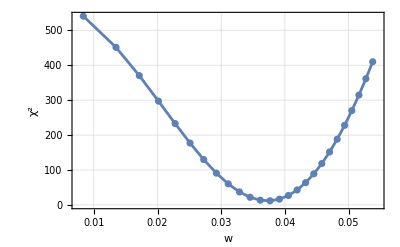

```mathematica
ha = Show[
ListLinePlot[
Transpose[{wvals,chisq}],
Frame->True,
FrameLabel->{"w",Superscript["χ","2"]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{{Min[wvals] - Min[wvals]/10,Max[wvals] + Min[wvals]/10},{Automatic,Automatic}}
],
ListPlot[Transpose[{wvals,chisq}]]
]
```

```mathematica
zm = zm/. FindMinimum[Interpolation[Transpose[{zms,chisq}]][zm],{zm,zms[[1]],zms[[-1]]}][[2]]
```

0.00298727

```mathematica
w = Interpolation[Transpose[{zms,wvals}]][zm]
```

0.0372931

```mathematica
ma1sfit = Interpolation[Transpose[{wvals,Flatten[ma1s]}]][w]
fa1fit = Interpolation[Transpose[{wvals,Flatten[fa1s]}]][w]
frhofit = Interpolation[Transpose[{wvals,Flatten[Frhos]}]][w]
```

1228.8

431.828

335.388

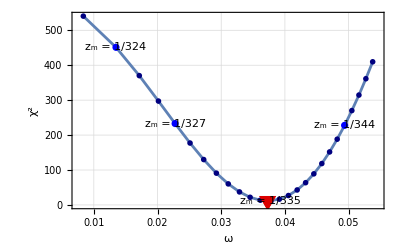

```mathematica
ha = Show[
ListLinePlot[

Transpose[{wvals,chisq}],
Frame->True,
FrameLabel->{Style["ω",Black,Bold,15],Style[Superscript["χ","2"],Black,Bold,15]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{{Min[wvals] - Min[wvals]/10,Max[wvals] + Min[wvals]/10},{Automatic,Automatic}}
],
ListPlot[Transpose[{wvals,chisq}],PlotStyle->Directive[Blend[{Blue,Black},1/2]],PlotMarkers->{{"OpenMarkers",5}}],
ListPlot[
Table[
{wvals[[i]],chisq[[i]]}
,{i,{2,5,13,22}} ],PlotStyle->Directive[Blue]],

ListPlot[{{w,Interpolation[Transpose[{wvals,chisq}]][w]}},PlotStyle->Directive[Blend[{Red,Black},1/7]],PlotMarkers->{{"▼",20}}],
(*Graphics[
Table[
Text[
Row[{Subscript["z","m"]," = ",zms[[i]]}],{wvals[[i]],chisq[[i]]},{0.6,-1.3}]
,{i,{2,5,13,22}} ]],*)
Graphics[
{
Text[
Row[{Subscript["z","m"]," = ",zms[[2]]}],{wvals[[2]],chisq[[2]]},{-1.5,0}],
Text[
Row[{Subscript["z","m"]," = ",zms[[5]]}],{wvals[[5]],chisq[[5]]},{-1.5,0}],
Text[
Row[{Subscript["z","m"]," = ",zms[[13]]}],{wvals[[13]],chisq[[13]]},{0,-1.5}],
Text[
Row[{Subscript["z","m"]," = ",zms[[22]]}],{wvals[[22]],chisq[[22]]},{1.5,0}]
}]
]
```

```mathematica
Export[NotebookDirectory[]<>"wvschisq.pdf",ha,ImageResolution->1000]
```

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\wvschisq.pdf

```mathematica
FindMinimum[Interpolation[Transpose[{wvals,chisq}]][wv],{wv,wvals[[1]],wvals[[-1]]}]
```

{11.6969,{wv→0.0372938}}

```mathematica
ma1sfit = Interpolation[Transpose[{wvals,Flatten[ma1s]}]][w]
fa1fit = Interpolation[Transpose[{wvals,Flatten[fa1s]}]][w]
frhofit = Interpolation[Transpose[{wvals,Flatten[Frhos]}]][w]
```

1228.8

431.828

335.388

```mathematica
wp = wv/. FindRoot[Interpolation[Transpose[{wvals,chisq}]][wv] - (Interpolation[Transpose[{wvals,chisq}]][w]+1),{wv,w,w + w/10}]
wm = wv /.FindRoot[Interpolation[Transpose[{wvals,chisq}]][wv] - (Interpolation[Transpose[{wvals,chisq}]][w]+1),{wv,w,w - w/10}]
```

0.0381336

0.0364414

```mathematica
{
Interpolation[Transpose[{wvals,Flatten[ma1s]}]][w] - Interpolation[Transpose[{wvals,Flatten[ma1s]}]][wm],
Interpolation[Transpose[{wvals,Flatten[ma1s]}]][w] - Interpolation[Transpose[{wvals,Flatten[ma1s]}]][wp]
}
```

{-5.31789,5.30949}

```mathematica
{
Interpolation[Transpose[{wvals,Flatten[fa1s]}]][w] - Interpolation[Transpose[{wvals,Flatten[fa1s]}]][wm],
Interpolation[Transpose[{wvals,Flatten[fa1s]}]][w] - Interpolation[Transpose[{wvals,Flatten[fa1s]}]][wp]
}
```

{-1.96411,1.93544}

```mathematica
{
Interpolation[Transpose[{wvals,Flatten[Frhos]}]][w] - Interpolation[Transpose[{wvals,Flatten[Frhos]}]][wm],
Interpolation[Transpose[{wvals,Flatten[Frhos]}]][w] - Interpolation[Transpose[{wvals,Flatten[Frhos]}]][wp]
}
```

{0.27482,-0.276866}